# Calendarización de Pruebas

## Claudio Mora Díaz - René Prieto

Acotación importante: los resultados aquí presentados, fueron calculados respecto a los obtenidos por nosotros por lo que, se recomienda, antes de experimentar con el código, leer los que se muestran, a fin de comprender su relación con el documento escrito.

```mathematica
(* Necesario para limpiar caché con variables y establecer directorio *)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## Demanda

En primer lugar, accedemos al archivo para extraer la información de la segunda hoja y crear el vector con la demanda.
Una acotación importante, proviene de notar que los ramos se encuentran enumerados según aparecen en las diferentes carreras, por lo que pueden haber múltiples entradas para un mismo nombre (una entrada por cada carrera, junto a su respectiva demanda). 
Para efectos prácticos, sin embargo, el mismo ramo se rinde todos los semestres, de este modo, necesitamos agrupar las entradas de una misma asignatura y sumar la demanda en cada currículo.
Todo esto se realiza en las celdas a continuación.

```mathematica
(* Importar el archivo excel con los datos *)
sheets =Drop[Drop[DeleteCases[Import["Datos.xlsx"][[2]],"",{2}],2],0,-1];
```

```mathematica
For[i=1,i<Length[sheets],i++,For[j=i+1,j<=Length[sheets],j++,
If[sheets[[j]][[1]]==sheets[[i]][[1]],(*Identifica los ramos con un mismo nombre*)
sheets[[i]][[2]]=sheets[[i]][[2]]+sheets[[j]][[2]];sheets=Drop[sheets,{j}]]]](*agrupa los ramos semejantes*)
sheets=Reverse[SortBy[sheets,Last]](*Ordena las asignaturas según la demanda*);
```

```mathematica
Print["El ramo con mayor demanda es ",sheets[[1]][[1]],". Y el ramo con menor demanda es ",sheets[[-1]][[1]],". Esto, de un total de ",Length[sheets]," asignaturas diferentes."]
```

El ramo con mayor demanda es Calculo I. Y el ramo con menor demanda es Diseño en Hormigon. Esto, de un total de 112 asignaturas diferentes.

Estos resultados nos sirven para dimensionar el número de alumnos por asignatura, así como para identificar fácilmente los cursos más potencialmente problemáticos (desde el punto de vista del aforo).

```mathematica
Print[sheets[[1;;10]]](*Las diez asignaturas con mayor demanda*)
```

{{Calculo I,316.},{Algebra,285.},{Fisica I,263.},{Introduccion Ingenieria,246.},{Mecanica,215.},{Contabilidad y Costos,176.},{Ingenieria Economica,169.},{Computacion II,168.},{Liderazgo y Trabajo en Equipo,167.},{Laboratorio de Fisica,167.}}

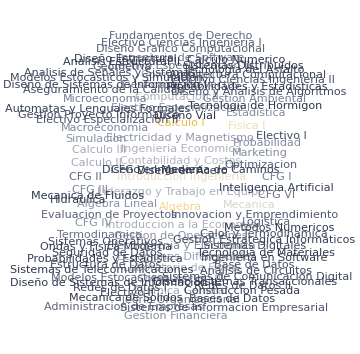

```mathematica
WordCloud[sheets,FontFamily->"Century Gothic",ColorFunction->ColorData["GrayYellowTones"]]
```

La razón de por qué esto es útil, proviene de la disponibilidad de salas; ahora que conocemos los ramos con mayor requerimiento de aforo, intentaremos llenar de forma avara las salas.

```mathematica
sals={{3,111},{7,55},{14,31}};
ramosgrandes=sheets[[1;;10]];
ramosgrandes=Transpose[Insert[ramosgrandes//Transpose,Table["s:",Length[ramosgrandes]],3]];
```

```mathematica
Do[
Module[{free=ramosgrandes[[i]][[2]]},
While[free>0,
If[sals[[1]][[1]]>0,sals[[1]][[1]]-=1;free-=111;ramosgrandes[[i]][[3]]=ramosgrandes[[i]][[3]]<>"L";Continue[],(*salas large*)
If[sals[[2]][[1]]>0,sals[[2]][[1]]-=1;free-=55;ramosgrandes[[i]][[3]]=ramosgrandes[[i]][[3]]<>"M";Continue[],(*salas medium*)
If[sals[[3]][[1]]>0,sals[[3]][[1]]-=1;free-=31;ramosgrandes[[i]][[3]]=ramosgrandes[[i]][[3]]<>"S";Continue[],(*salas small*)
Break[]]
]
]
]
]
,{i,1,Length[ramosgrandes]}]
```

```mathematica
ramosgrandes
```

{{Calculo I,316.,s:LLL},{Algebra,285.,s:MMMMMM},{Fisica I,263.,s:MSSSSSSS},{Introduccion Ingenieria,246.,s:SSSSSSS},{Mecanica,215.,s:},{Contabilidad y Costos,176.,s:},{Ingenieria Economica,169.,s:},{Computacion II,168.,s:},{Liderazgo y Trabajo en Equipo,167.,s:},{Laboratorio de Fisica,167.,s:}}

Este resultado no es tan inesperado; estamos intentando verificar que con la cantidad de salas disponible, y en consideración de la capacidad de cada sala, no es posible albergar una indefinida cantidad de alumnos, en particular, hemos podido albergar por completo solo a 3 asignaturas, pudiendo recibir a gran parte de una cuarta asignatura, pero nos quedamos sin espacios disponibles.
De esta situación, es que surge la idea de abordar la asignación de salas desde otro acercamiento.

## Aforo

Supongamos ahora que existen “asignaturas perfectas”, cuya demanda (y por ende, necesidad total de aforo en salas) es una combinación lineal de los valores discretos que cada tipo de sala puede albergar.

d_i=a·L+b·M+c·S

d_i:demanda de ramo
a,b,c:coeficientes enteros
L,M,S:aforo en diferentes salas

Con esta idea en mente, verificamos si existe alguna asignatura que cumpla con ser “perfecta” resolviendo la ecuación diofántica.

```mathematica
combpos={};
Do[
If[FindInstance[Round[sheets[[i]][[2]]]==a*111+b*55+c*31,{a,b,c},NonNegativeIntegers]!={},AppendTo[combpos,{sheets[[i]][[1]],FindInstance[Round[sheets[[i]][[2]]]==a*111+b*55+c*31,{a,b,c},NonNegativeIntegers]}]]
,{i,1,112}]
combpos
```

{{Introduccion a la Economia,{{a→0,b→3,c→0}}},{Electrotecnia y Electronica,{{a→0,b→0,c→4}}},{Teoria Organizacional,{{a→0,b→2,c→0}}},{Redes de Datos II,{{a→0,b→1,c→0}}},{Analisis de Circuitos,{{a→0,b→1,c→0}}},{Diseño de Sistemas de Informacion II,{{a→0,b→0,c→1}}}}

Esto nos muestra las asignaturas cuya demanda se ajusta a alguna combinación lineal discreta de las salas. 
Aunque no exista alguna combinación que nos entregue exactamente el número de alumnos para el resto de los ramos, debemos admitir cierto rango de libertad por la inexactitud proveniente de utilizar la estadística de la media. Y de todas formas, es un resultado aceptable que “sobren” una o dos sillas en la sala que se rinde cada prueba.
Por esto, probaremos admitiendo la posibilidad de que sobre una silla en el aula.

```mathematica
Do[
If[FindInstance[Round[sheets[[i]][[2]]]==a*111+b*55+c*31-1,{a,b,c},NonNegativeIntegers]!={},AppendTo[combpos,{sheets[[i]][[1]],FindInstance[Round[sheets[[i]][[2]]]==a*111+b*55+c*31-1,{a,b,c},NonNegativeIntegers]}]]
,{i,1,112}]
combpos
```

{{Introduccion a la Economia,{{a→0,b→3,c→0}}},{Electrotecnia y Electronica,{{a→0,b→0,c→4}}},{Teoria Organizacional,{{a→0,b→2,c→0}}},{Redes de Datos II,{{a→0,b→1,c→0}}},{Analisis de Circuitos,{{a→0,b→1,c→0}}},{Diseño de Sistemas de Informacion II,{{a→0,b→0,c→1}}},{Introduccion a la Economia,{{a→1,b→1,c→0}}},{CFG III,{{a→0,b→0,c→4}}},{Teoria Organizacional,{{a→1,b→0,c→0}}},{Logistica,{{a→0,b→0,c→3}}},{Electivo II,{{a→0,b→0,c→2}}},{Redes de Datos I,{{a→0,b→1,c→0}}},{CFG V,{{a→0,b→1,c→0}}},{Tecnologia de Hormigon,{{a→0,b→0,c→1}}},{Diseño en Acero,{{a→0,b→0,c→1}}}}

Ahora hemos cubierto más ramos al admitir la posibilidad de que existan sillas vacías. Esta idea la podemos expandir lo suficiente para encontrar el óptimo de cada asignatura.
Recordemos que con estos cálculos, estamos obteniendo la forma más óptima de distribuir los alumnos para cada asignatura, sin considerar la cantidad de salas o los módulos horarios: simplemente queremos conocer cómo luce el óptimo de cada asignatura.

En el código anterior, nos limitamos a admitir una sola silla sobrante. Ahora, sin embargo, expandiremos esta restricción lo suficiente para encontrar la mejor combinación posible para todas las asignaturas.

```mathematica
combpos={};
Do[
For[p=0,p<=25,p++,
Module[{l=FindInstance[Round[sheets[[i]][[2]]]==L*111+M*55+S*31-p,{L,M,S},NonNegativeIntegers]},
If[l!={},AppendTo[combpos,{sheets[[i]][[1]],l,StringForm["Con `` sillas desocupadas",p]}];Break[]]
]
]
,{i,1,Length[sheets]}]
```

Con esto, como se mencionó anteriormente, hemos encontrado la configuración de salas óptima para cada asignatura. Que podemos visualizar:

```mathematica
(*configuraciones para ajustar la estética y visualizar en una tabla los resultados*)
tabla=combpos;
ReplacePart[Insert[Grid[tabla],{Background->{None,{{RGBColor[0.25,0.25,0.25],Black}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}},2],1->Prepend[tabla,{"Asignatura","Salas","Ajuste"}]]
```

Asignatura | Salas | Ajuste
Calculo I | {{L→0,M→3,S→5}} | Con 4 sillas desocupadas
Algebra | {{L→0,M→3,S→4}} | Con 4 sillas desocupadas
Fisica I | {{L→0,M→2,S→5}} | Con 2 sillas desocupadas
Introduccion Ingenieria | {{L→0,M→0,S→8}} | Con 2 sillas desocupadas
Mecanica | {{L→0,M→0,S→7}} | Con 2 sillas desocupadas
Contabilidad y Costos | {{L→0,M→1,S→4}} | Con 3 sillas desocupadas
Ingenieria Economica | {{L→0,M→2,S→2}} | Con 3 sillas desocupadas
Computacion II | {{L→0,M→2,S→2}} | Con 4 sillas desocupadas
Liderazgo y Trabajo en Equipo | {{L→0,M→2,S→2}} | Con 5 sillas desocupadas
Laboratorio de Fisica | {{L→0,M→2,S→2}} | Con 5 sillas desocupadas
Introduccion a la Economia | {{L→0,M→3,S→0}} | Con 0 sillas desocupadas
Calculo III | {{L→0,M→3,S→0}} | Con 4 sillas desocupadas
Quimica General | {{L→0,M→3,S→0}} | Con 5 sillas desocupadas
Calculo II | {{L→0,M→3,S→0}} | Con 5 sillas desocupadas
Ecuaciones Diferenciales | {{L→0,M→0,S→5}} | Con 5 sillas desocupadas
Computacion I | {{L→0,M→0,S→5}} | Con 5 sillas desocupadas
Computacion III | {{L→0,M→0,S→5}} | Con 6 sillas desocupadas
Electricidad y Magnetismo | {{L→0,M→1,S→3}} | Con 5 sillas desocupadas
Gestion de Operaciones | {{L→0,M→2,S→1}} | Con 3 sillas desocupadas
CFG IV | {{L→0,M→2,S→1}} | Con 3 sillas desocupadas
Simulacion | {{L→0,M→2,S→1}} | Con 4 sillas desocupadas
Algebra Lineal | {{L→0,M→2,S→1}} | Con 5 sillas desocupadas
Electivo Especializacion I | {{L→0,M→2,S→1}} | Con 7 sillas desocupadas
Gestion Financiera | {{L→0,M→2,S→1}} | Con 8 sillas desocupadas
Probabilidad | {{L→0,M→2,S→1}} | Con 9 sillas desocupadas
Estadistica | {{L→0,M→2,S→1}} | Con 9 sillas desocupadas
Marketing | {{L→0,M→2,S→1}} | Con 10 sillas desocupadas
Macroeconomia | {{L→0,M→2,S→1}} | Con 14 sillas desocupadas
Gestion de Proyectos | {{L→0,M→2,S→1}} | Con 14 sillas desocupadas
Electrotecnia y Electronica | {{L→0,M→0,S→4}} | Con 0 sillas desocupadas
CFG III | {{L→0,M→0,S→4}} | Con 1 sillas desocupadas
Gestion Ambiental | {{L→0,M→0,S→4}} | Con 2 sillas desocupadas
Microeconomia | {{L→0,M→0,S→4}} | Con 6 sillas desocupadas
CFG I | {{L→0,M→1,S→2}} | Con 3 sillas desocupadas
Ingenieria de Software | {{L→0,M→1,S→2}} | Con 4 sillas desocupadas
Teoria Organizacional | {{L→0,M→2,S→0}} | Con 0 sillas desocupadas
Electivo Especializacion III | {{L→0,M→2,S→0}} | Con 5 sillas desocupadas
CFG VI | {{L→0,M→2,S→0}} | Con 5 sillas desocupadas
Termodinamica | {{L→0,M→2,S→0}} | Con 6 sillas desocupadas
Fundamentos de Derecho | {{L→0,M→2,S→0}} | Con 15 sillas desocupadas
CFG II | {{L→0,M→2,S→0}} | Con 15 sillas desocupadas
Logistica | {{L→0,M→0,S→3}} | Con 1 sillas desocupadas
Administracion de Empresas | {{L→0,M→0,S→3}} | Con 2 sillas desocupadas
Modelos Estocasticos | {{L→0,M→0,S→3}} | Con 4 sillas desocupadas
Evaluacion de Proyectos | {{L→0,M→0,S→3}} | Con 5 sillas desocupadas
Diseño Grafico Computacional | {{L→0,M→0,S→3}} | Con 5 sillas desocupadas
Optimizacion | {{L→0,M→1,S→1}} | Con 3 sillas desocupadas
Electivo Ciencias Ingenieria I | {{L→0,M→1,S→1}} | Con 4 sillas desocupadas
Geometria | {{L→0,M→1,S→1}} | Con 10 sillas desocupadas
Innovacion y Emprendimiento | {{L→0,M→1,S→1}} | Con 11 sillas desocupadas
Electivo Especializacion II | {{L→0,M→1,S→1}} | Con 13 sillas desocupadas
Sistemas de Informacion Empresarial | {{L→0,M→1,S→1}} | Con 14 sillas desocupadas
Base de Datos | {{L→0,M→1,S→1}} | Con 14 sillas desocupadas
Electivo Ciencias Ingenieria II | {{L→0,M→1,S→1}} | Con 16 sillas desocupadas
Calor y Termodinamica | {{L→0,M→1,S→1}} | Con 19 sillas desocupadas
Electivo I | {{L→0,M→1,S→1}} | Con 23 sillas desocupadas
Electivo II | {{L→0,M→0,S→2}} | Con 1 sillas desocupadas
Sistemas Digitales | {{L→0,M→0,S→2}} | Con 2 sillas desocupadas
Sistemas de Comunicación Digital | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Modelos Estocasticos y Simulacion | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Diseño y Analisis de Algoritmos | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Aseguramiento de la Calidad | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Sistemas Operativos | {{L→0,M→0,S→2}} | Con 4 sillas desocupadas
Estructura de Datos | {{L→0,M→0,S→2}} | Con 5 sillas desocupadas
Arquitectura Computacional | {{L→0,M→0,S→2}} | Con 5 sillas desocupadas
Analisis de Señales y Sistemas | {{L→0,M→0,S→2}} | Con 6 sillas desocupadas
Redes de Datos II | {{L→0,M→1,S→0}} | Con 0 sillas desocupadas
Analisis de Circuitos | {{L→0,M→1,S→0}} | Con 0 sillas desocupadas
Redes de Datos I | {{L→0,M→1,S→0}} | Con 1 sillas desocupadas
CFG V | {{L→0,M→1,S→0}} | Con 1 sillas desocupadas
Seguridad de Datos | {{L→0,M→1,S→0}} | Con 2 sillas desocupadas
Gestion Proyecto Informatico | {{L→0,M→1,S→0}} | Con 2 sillas desocupadas
Automatas y Lenguajes Formales | {{L→0,M→1,S→0}} | Con 10 sillas desocupadas
Diseño de Sistemas de Informacion I | {{L→0,M→1,S→0}} | Con 11 sillas desocupadas
Sistemas Distribuidos | {{L→0,M→1,S→0}} | Con 12 sillas desocupadas
Ondas y Fisica Moderna | {{L→0,M→1,S→0}} | Con 12 sillas desocupadas
Gestion Estrategica Informaticos | {{L→0,M→1,S→0}} | Con 12 sillas desocupadas
Inteligencia Artificial | {{L→0,M→1,S→0}} | Con 14 sillas desocupadas
Tecnologia del Asfalto | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Hidraulica | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Diseño Sistemas Transaccionales | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Bases de Datos | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Probabilidades y Estadistica | {{L→0,M→1,S→0}} | Con 17 sillas desocupadas
Construccion Pesada | {{L→0,M→1,S→0}} | Con 17 sillas desocupadas
Ingenieria en Software | {{L→0,M→1,S→0}} | Con 18 sillas desocupadas
Ingenieria de Caminos | {{L→0,M→1,S→0}} | Con 19 sillas desocupadas
Diseño en Madera | {{L→0,M→1,S→0}} | Con 19 sillas desocupadas
Sistemas de Telecomunicaciones | {{L→0,M→1,S→0}} | Con 20 sillas desocupadas
Probabilidades y Estadisticas | {{L→0,M→1,S→0}} | Con 20 sillas desocupadas
Diseño Estructural | {{L→0,M→1,S→0}} | Con 20 sillas desocupadas
Tecnologia de Materiales | {{L→0,M→1,S→0}} | Con 21 sillas desocupadas
Metodos Numericos | {{L→0,M→1,S→0}} | Con 21 sillas desocupadas
Diseño Vial | {{L→0,M→1,S→0}} | Con 22 sillas desocupadas
Calculo Numerico | {{L→0,M→1,S→0}} | Con 22 sillas desocupadas
Analisis Estructural II | {{L→0,M→1,S→0}} | Con 22 sillas desocupadas
Diseño de Sistemas de Informacion II | {{L→0,M→0,S→1}} | Con 0 sillas desocupadas
Tecnologia de Hormigon | {{L→0,M→0,S→1}} | Con 1 sillas desocupadas
Diseño en Acero | {{L→0,M→0,S→1}} | Con 1 sillas desocupadas
Mecanica de Solidos | {{L→0,M→0,S→1}} | Con 2 sillas desocupadas
Mecanica de Fluidos | {{L→0,M→0,S→1}} | Con 2 sillas desocupadas
Analisis Estructural I | {{L→0,M→0,S→1}} | Con 3 sillas desocupadas
Estructuras de Acero | {{L→0,M→0,S→1}} | Con 4 sillas desocupadas
Diseño Hidraulico | {{L→0,M→0,S→1}} | Con 4 sillas desocupadas
Ingenieria Antisismica | {{L→0,M→0,S→1}} | Con 5 sillas desocupadas
Topografia | {{L→0,M→0,S→1}} | Con 7 sillas desocupadas
Optimizacion I | {{L→0,M→0,S→1}} | Con 8 sillas desocupadas
Modelos de Transporte | {{L→0,M→0,S→1}} | Con 8 sillas desocupadas
Mecanica de Suelos | {{L→0,M→0,S→1}} | Con 8 sillas desocupadas
Fundaciones | {{L→0,M→0,S→1}} | Con 9 sillas desocupadas
Estatica Aplicada | {{L→0,M→0,S→1}} | Con 9 sillas desocupadas
Edificacion | {{L→0,M→0,S→1}} | Con 10 sillas desocupadas
Diseño en Hormigon | {{L→0,M→0,S→1}} | Con 10 sillas desocupadas

En esta tabla se visualiza una imprecisión de este acercamiento; aunque hemos efectivamente encontrado una combinación que minimiza el número de sillas desocupadas, se verifica que en ningún caso, se utilizan las salas Large. Para solucionar esto, aplicaremos nuevamente el cálculo de la ecuación diofántica, pero forzado a que, si un ramo puede utilizar una sala Large (es decir, tiene al menos 111 alumnos), entonces debe usar al menos una de ellas.

```mathematica
combpos={};
Do[
For[p=0,p<=30,p++,
If[sheets[[i]][[2]]>=111,Module[{l=FindInstance[L>=1&&Round[sheets[[i]][[2]]]==L*111+M*55+S*31-p,{L,M,S},NonNegativeIntegers]},
If[l!={},AppendTo[combpos,{sheets[[i]][[1]],l,StringForm["Con `` sillas desocupadas",p]}];Break[]]
],Module[{l=FindInstance[Round[sheets[[i]][[2]]]==L*111+M*55+S*31-p,{L,M,S},NonNegativeIntegers]},
If[l!={},AppendTo[combpos,{sheets[[i]][[1]],l,StringForm["Con `` sillas desocupadas",p]}];Break[]]
]]
]
,{i,1,Length[sheets]}]
tabla=combpos;
ReplacePart[Insert[Grid[tabla],{Background->{None,{{RGBColor[0.25,0.25,0.25],Black}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}},2],1->Prepend[tabla,{"Asignatura","Salas","Ajuste"}]]
```

Asignatura | Salas | Ajuste
Calculo I | {{L→1,M→1,S→5}} | Con 5 sillas desocupadas
Algebra | {{L→1,M→1,S→4}} | Con 5 sillas desocupadas
Fisica I | {{L→1,M→0,S→5}} | Con 3 sillas desocupadas
Introduccion Ingenieria | {{L→1,M→2,S→1}} | Con 6 sillas desocupadas
Mecanica | {{L→1,M→2,S→0}} | Con 6 sillas desocupadas
Contabilidad y Costos | {{L→1,M→1,S→1}} | Con 21 sillas desocupadas
Ingenieria Economica | {{L→1,M→0,S→2}} | Con 4 sillas desocupadas
Computacion II | {{L→1,M→0,S→2}} | Con 5 sillas desocupadas
Liderazgo y Trabajo en Equipo | {{L→1,M→0,S→2}} | Con 6 sillas desocupadas
Laboratorio de Fisica | {{L→1,M→0,S→2}} | Con 6 sillas desocupadas
Introduccion a la Economia | {{L→1,M→1,S→0}} | Con 1 sillas desocupadas
Calculo III | {{L→1,M→1,S→0}} | Con 5 sillas desocupadas
Quimica General | {{L→1,M→1,S→0}} | Con 6 sillas desocupadas
Calculo II | {{L→1,M→1,S→0}} | Con 6 sillas desocupadas
Ecuaciones Diferenciales | {{L→1,M→1,S→0}} | Con 16 sillas desocupadas
Computacion I | {{L→1,M→1,S→0}} | Con 16 sillas desocupadas
Computacion III | {{L→1,M→1,S→0}} | Con 17 sillas desocupadas
Electricidad y Magnetismo | {{L→1,M→1,S→0}} | Con 23 sillas desocupadas
Gestion de Operaciones | {{L→1,M→0,S→1}} | Con 4 sillas desocupadas
CFG IV | {{L→1,M→0,S→1}} | Con 4 sillas desocupadas
Simulacion | {{L→1,M→0,S→1}} | Con 5 sillas desocupadas
Algebra Lineal | {{L→1,M→0,S→1}} | Con 6 sillas desocupadas
Electivo Especializacion I | {{L→1,M→0,S→1}} | Con 8 sillas desocupadas
Gestion Financiera | {{L→1,M→0,S→1}} | Con 9 sillas desocupadas
Probabilidad | {{L→1,M→0,S→1}} | Con 10 sillas desocupadas
Estadistica | {{L→1,M→0,S→1}} | Con 10 sillas desocupadas
Marketing | {{L→1,M→0,S→1}} | Con 11 sillas desocupadas
Macroeconomia | {{L→1,M→0,S→1}} | Con 15 sillas desocupadas
Gestion de Proyectos | {{L→1,M→0,S→1}} | Con 15 sillas desocupadas
Electrotecnia y Electronica | {{L→1,M→0,S→1}} | Con 18 sillas desocupadas
CFG III | {{L→1,M→0,S→1}} | Con 19 sillas desocupadas
Gestion Ambiental | {{L→1,M→0,S→1}} | Con 20 sillas desocupadas
Microeconomia | {{L→1,M→0,S→1}} | Con 24 sillas desocupadas
CFG I | {{L→1,M→0,S→1}} | Con 28 sillas desocupadas
Ingenieria de Software | {{L→1,M→0,S→1}} | Con 29 sillas desocupadas
Teoria Organizacional | {{L→0,M→2,S→0}} | Con 0 sillas desocupadas
Electivo Especializacion III | {{L→0,M→2,S→0}} | Con 5 sillas desocupadas
CFG VI | {{L→0,M→2,S→0}} | Con 5 sillas desocupadas
Termodinamica | {{L→0,M→2,S→0}} | Con 6 sillas desocupadas
Fundamentos de Derecho | {{L→0,M→2,S→0}} | Con 15 sillas desocupadas
CFG II | {{L→0,M→2,S→0}} | Con 15 sillas desocupadas
Logistica | {{L→0,M→0,S→3}} | Con 1 sillas desocupadas
Administracion de Empresas | {{L→0,M→0,S→3}} | Con 2 sillas desocupadas
Modelos Estocasticos | {{L→0,M→0,S→3}} | Con 4 sillas desocupadas
Evaluacion de Proyectos | {{L→0,M→0,S→3}} | Con 5 sillas desocupadas
Diseño Grafico Computacional | {{L→0,M→0,S→3}} | Con 5 sillas desocupadas
Optimizacion | {{L→0,M→1,S→1}} | Con 3 sillas desocupadas
Electivo Ciencias Ingenieria I | {{L→0,M→1,S→1}} | Con 4 sillas desocupadas
Geometria | {{L→0,M→1,S→1}} | Con 10 sillas desocupadas
Innovacion y Emprendimiento | {{L→0,M→1,S→1}} | Con 11 sillas desocupadas
Electivo Especializacion II | {{L→0,M→1,S→1}} | Con 13 sillas desocupadas
Sistemas de Informacion Empresarial | {{L→0,M→1,S→1}} | Con 14 sillas desocupadas
Base de Datos | {{L→0,M→1,S→1}} | Con 14 sillas desocupadas
Electivo Ciencias Ingenieria II | {{L→0,M→1,S→1}} | Con 16 sillas desocupadas
Calor y Termodinamica | {{L→0,M→1,S→1}} | Con 19 sillas desocupadas
Electivo I | {{L→0,M→1,S→1}} | Con 23 sillas desocupadas
Electivo II | {{L→0,M→0,S→2}} | Con 1 sillas desocupadas
Sistemas Digitales | {{L→0,M→0,S→2}} | Con 2 sillas desocupadas
Sistemas de Comunicación Digital | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Modelos Estocasticos y Simulacion | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Diseño y Analisis de Algoritmos | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Aseguramiento de la Calidad | {{L→0,M→0,S→2}} | Con 3 sillas desocupadas
Sistemas Operativos | {{L→0,M→0,S→2}} | Con 4 sillas desocupadas
Estructura de Datos | {{L→0,M→0,S→2}} | Con 5 sillas desocupadas
Arquitectura Computacional | {{L→0,M→0,S→2}} | Con 5 sillas desocupadas
Analisis de Señales y Sistemas | {{L→0,M→0,S→2}} | Con 6 sillas desocupadas
Redes de Datos II | {{L→0,M→1,S→0}} | Con 0 sillas desocupadas
Analisis de Circuitos | {{L→0,M→1,S→0}} | Con 0 sillas desocupadas
Redes de Datos I | {{L→0,M→1,S→0}} | Con 1 sillas desocupadas
CFG V | {{L→0,M→1,S→0}} | Con 1 sillas desocupadas
Seguridad de Datos | {{L→0,M→1,S→0}} | Con 2 sillas desocupadas
Gestion Proyecto Informatico | {{L→0,M→1,S→0}} | Con 2 sillas desocupadas
Automatas y Lenguajes Formales | {{L→0,M→1,S→0}} | Con 10 sillas desocupadas
Diseño de Sistemas de Informacion I | {{L→0,M→1,S→0}} | Con 11 sillas desocupadas
Sistemas Distribuidos | {{L→0,M→1,S→0}} | Con 12 sillas desocupadas
Ondas y Fisica Moderna | {{L→0,M→1,S→0}} | Con 12 sillas desocupadas
Gestion Estrategica Informaticos | {{L→0,M→1,S→0}} | Con 12 sillas desocupadas
Inteligencia Artificial | {{L→0,M→1,S→0}} | Con 14 sillas desocupadas
Tecnologia del Asfalto | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Hidraulica | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Diseño Sistemas Transaccionales | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Bases de Datos | {{L→0,M→1,S→0}} | Con 16 sillas desocupadas
Probabilidades y Estadistica | {{L→0,M→1,S→0}} | Con 17 sillas desocupadas
Construccion Pesada | {{L→0,M→1,S→0}} | Con 17 sillas desocupadas
Ingenieria en Software | {{L→0,M→1,S→0}} | Con 18 sillas desocupadas
Ingenieria de Caminos | {{L→0,M→1,S→0}} | Con 19 sillas desocupadas
Diseño en Madera | {{L→0,M→1,S→0}} | Con 19 sillas desocupadas
Sistemas de Telecomunicaciones | {{L→0,M→1,S→0}} | Con 20 sillas desocupadas
Probabilidades y Estadisticas | {{L→0,M→1,S→0}} | Con 20 sillas desocupadas
Diseño Estructural | {{L→0,M→1,S→0}} | Con 20 sillas desocupadas
Tecnologia de Materiales | {{L→0,M→1,S→0}} | Con 21 sillas desocupadas
Metodos Numericos | {{L→0,M→1,S→0}} | Con 21 sillas desocupadas
Diseño Vial | {{L→0,M→1,S→0}} | Con 22 sillas desocupadas
Calculo Numerico | {{L→0,M→1,S→0}} | Con 22 sillas desocupadas
Analisis Estructural II | {{L→0,M→1,S→0}} | Con 22 sillas desocupadas
Diseño de Sistemas de Informacion II | {{L→0,M→0,S→1}} | Con 0 sillas desocupadas
Tecnologia de Hormigon | {{L→0,M→0,S→1}} | Con 1 sillas desocupadas
Diseño en Acero | {{L→0,M→0,S→1}} | Con 1 sillas desocupadas
Mecanica de Solidos | {{L→0,M→0,S→1}} | Con 2 sillas desocupadas
Mecanica de Fluidos | {{L→0,M→0,S→1}} | Con 2 sillas desocupadas
Analisis Estructural I | {{L→0,M→0,S→1}} | Con 3 sillas desocupadas
Estructuras de Acero | {{L→0,M→0,S→1}} | Con 4 sillas desocupadas
Diseño Hidraulico | {{L→0,M→0,S→1}} | Con 4 sillas desocupadas
Ingenieria Antisismica | {{L→0,M→0,S→1}} | Con 5 sillas desocupadas
Topografia | {{L→0,M→0,S→1}} | Con 7 sillas desocupadas
Optimizacion I | {{L→0,M→0,S→1}} | Con 8 sillas desocupadas
Modelos de Transporte | {{L→0,M→0,S→1}} | Con 8 sillas desocupadas
Mecanica de Suelos | {{L→0,M→0,S→1}} | Con 8 sillas desocupadas
Fundaciones | {{L→0,M→0,S→1}} | Con 9 sillas desocupadas
Estatica Aplicada | {{L→0,M→0,S→1}} | Con 9 sillas desocupadas
Edificacion | {{L→0,M→0,S→1}} | Con 10 sillas desocupadas
Diseño en Hormigon | {{L→0,M→0,S→1}} | Con 10 sillas desocupadas

Esta es una tabla que nos sintetiza los resultados óptimos de cada asignatura, e indica qué tan bueno es el resultado en formato de “sillas desocupadas”. Antes de continuar, limpiaremos un poco el resultado y transformaremos las asignaciones en un vector, con cada componente representando las salas Large, Medium y Small, respectivamente. Además, eliminaremos el dato que nos indica las sillas desocupadas.

```mathematica
salasoptimas=combpos;dic=<|"nulo"->{0,0,0}|>;
Do[salasoptimas[[ele]][[2]]=salasoptimas[[ele]][[2]][[1]][[All,2]];salasoptimas[[ele]]=Most[salasoptimas[[ele]]],{ele,1,Length[salasoptimas]}]
 Do[AppendTo[dic,Association[salasoptimas[[i]][[1]]->salasoptimas[[i]][[2]]]],{i,1,Length[salasoptimas]}]
(*forma final de cada ramo*)
```

Este es el formato final con que se encuentran almacenadas las asignaturas: {nombre, { L , M , S } }.

## Agrupaciones

Ahora importamos las mallas de las carreras. Visualizaremos la rejilla de cada una.

```mathematica
l=Import["Datos.xlsx"];
industrial=Table[Table[l[[1,f,c]],{f,3,8}],{c,3,12}];(*Transformar la tabla de excel en una lista*)
computacion=Table[Table[l[[1,f,c]],{f,12,17}],{c,3,12}];(*Cada componente de la lista representa un semestre distinto*)
obrasciv=Table[Table[l[[1,f,c]],{f,21,26}],{c,3,12}];(*Y tiene dentro, todos los ramos de ese semestre*)
Print["Carrera Industrial"]
Grid[industrial//Transpose,Frame->All,FrameStyle->LightGray,Background->RGBColor[0.11,0.,0.49],ItemSize->{Automatic,0}]
Print["Carrera Computación"]
Grid[computacion//Transpose,Frame->All,FrameStyle->LightGray,Background->RGBColor[0.51,0.09,0.],ItemSize->{Automatic,0}]
Print["Carrera Obras Civiles"]
Grid[obrasciv//Transpose,Frame->All,FrameStyle->LightGray,Background->RGBColor[0.59,0.42,0.],ItemSize->{Automatic,0}]
```

Carrera Industrial

Algebra | Algebra Lineal | Ecuaciones Diferenciales | Probabilidad | Estadistica | Microeconomia | Simulacion | Macroeconomia | Gestion Ambiental | Liderazgo y Trabajo en Equipo
Calculo I | Calculo II | Calculo III | Quimica General | Introduccion a la Economia | Modelos Estocasticos | Teoria Organizacional | Gestion Financiera | Evaluacion de Proyectos | Marketing
Fisica I | Mecanica | Electricidad y Magnetismo | Termodinamica | Optimizacion | Electrotecnia y Electronica | Base de Datos | Logistica | Sistemas de Informacion Empresarial | Fundamentos de Derecho
Introduccion Ingenieria | Laboratorio de Fisica | Electivo Ciencias Ingenieria I | Electivo Ciencias Ingenieria II | Contabilidad y Costos | Ingenieria Economica | Gestion de Operaciones | CFG IV | Gestion de Proyectos | Ingenieria de Software
Geometria | Computacion I | Computacion II | Computacion III | CFG I | CFG II | CFG III | Electivo Especializacion I | CFG V | CFG VI
 |  |  |  |  |  |  |  | Electivo Especializacion II | Electivo Especializacion III

Carrera Computación

Algebra | Algebra Lineal | Ecuaciones Diferenciales | Metodos Numericos | Analisis de Señales y Sistemas | Sistemas de Comunicación Digital | Redes de Datos I | Redes de Datos II | Seguridad de Datos | Sistemas de Telecomunicaciones
Calculo I | Calculo II | Calculo III | Electricidad y Magnetismo | Analisis de Circuitos | Arquitectura Computacional | Modelos Estocasticos y Simulacion | Diseño Sistemas Transaccionales | Inteligencia Artificial | Electivo I
Fisica I | Mecanica | Calor y Termodinamica | Ondas y Fisica Moderna | Sistemas Digitales | Sistemas Operativos | Sistemas Distribuidos | Diseño de Sistemas de Informacion I | Diseño de Sistemas de Informacion II | Aseguramiento de la Calidad
Introduccion Ingenieria | Laboratorio de Fisica | Probabilidades y Estadistica | Estructura de Datos | Bases de Datos | Automatas y Lenguajes Formales | Ingenieria en Software | Gestion Proyecto Informatico | Gestion Estrategica Informaticos | Electivo II
Computacion I | Computacion II | Computacion III | Diseño y Analisis de Algoritmos | Introduccion a la Economia | Administracion de Empresas | Contabilidad y Costos | Ingenieria Economica | Liderazgo y Trabajo en Equipo | Innovacion y Emprendimiento
 |  | Diseño Grafico Computacional |  | CFG I | CFG II | CFG III | CFG IV | CFG V | CFG VI

Carrera Obras Civiles

Algebra | Algebra Lineal | Calculo III | Calculo Numerico | Optimizacion I | Hidraulica | Modelos de Transporte | Ingenieria de Caminos | Diseño en Madera | Construccion Pesada
Calculo I | Calculo II | Ecuaciones Diferenciales | Probabilidades y Estadisticas | Mecanica de Fluidos | Analisis Estructural II | Mecanica de Suelos | Ingenieria Antisismica | Diseño en Hormigon | Estructuras de Acero
Fisica I | Mecanica | Calor y Termodinamica | Electricidad y Magnetismo | Analisis Estructural I | Diseño Estructural | Tecnologia de Hormigon | Fundaciones | Diseño en Acero | Diseño Hidraulico
Introduccion Ingenieria | Laboratorio de Fisica | Diseño Grafico Computacional | Tecnologia de Materiales | Tecnologia del Asfalto | Edificacion | Electivo I | Gestion de Operaciones | Electivo II | Diseño Vial
Computacion I | Computacion II | Quimica General | Topografia | Administracion de Empresas | Introduccion a la Economia | Contabilidad y Costos | Liderazgo y Trabajo en Equipo | Ingenieria Economica | Innovacion y Emprendimiento
 |  | Estatica Aplicada | Mecanica de Solidos | CFG I | CFG II | CFG III | CFG IV | CFG V | CFG VI

Si a esta cuadrícula le agregamos los vectores con la configuración de salas óptima para cada ramo, se visualizaría algo como lo siguiente.

```mathematica
GFindustrial=industrial;
Do[If[GFindustrial[[i]][[j]]!="",GFindustrial[[i]][[j]]={GFindustrial[[i]][[j]],dic[[GFindustrial[[i]][[j]]]]}],{i,1,Length[industrial]},{j,1,Length[industrial[[i]]]}]
Grid[GFindustrial//Transpose,Frame->All,FrameStyle->LightGray,Background->RGBColor[0.11,0.,0.49],ItemSize->{Automatic,0}]
```

{Algebra,{1,1,4}} | {Algebra Lineal,{1,0,1}} | {Ecuaciones Diferenciales,{1,1,0}} | {Probabilidad,{1,0,1}} | {Estadistica,{1,0,1}} | {Microeconomia,{1,0,1}} | {Simulacion,{1,0,1}} | {Macroeconomia,{1,0,1}} | {Gestion Ambiental,{1,0,1}} | {Liderazgo y Trabajo en Equipo,{1,0,2}}
{Calculo I,{1,1,5}} | {Calculo II,{1,1,0}} | {Calculo III,{1,1,0}} | {Quimica General,{1,1,0}} | {Introduccion a la Economia,{1,1,0}} | {Modelos Estocasticos,{0,0,3}} | {Teoria Organizacional,{0,2,0}} | {Gestion Financiera,{1,0,1}} | {Evaluacion de Proyectos,{0,0,3}} | {Marketing,{1,0,1}}
{Fisica I,{1,0,5}} | {Mecanica,{1,2,0}} | {Electricidad y Magnetismo,{1,1,0}} | {Termodinamica,{0,2,0}} | {Optimizacion,{0,1,1}} | {Electrotecnia y Electronica,{1,0,1}} | {Base de Datos,{0,1,1}} | {Logistica,{0,0,3}} | {Sistemas de Informacion Empresarial,{0,1,1}} | {Fundamentos de Derecho,{0,2,0}}
{Introduccion Ingenieria,{1,2,1}} | {Laboratorio de Fisica,{1,0,2}} | {Electivo Ciencias Ingenieria I,{0,1,1}} | {Electivo Ciencias Ingenieria II,{0,1,1}} | {Contabilidad y Costos,{1,1,1}} | {Ingenieria Economica,{1,0,2}} | {Gestion de Operaciones,{1,0,1}} | {CFG IV,{1,0,1}} | {Gestion de Proyectos,{1,0,1}} | {Ingenieria de Software,{1,0,1}}
{Geometria,{0,1,1}} | {Computacion I,{1,1,0}} | {Computacion II,{1,0,2}} | {Computacion III,{1,1,0}} | {CFG I,{1,0,1}} | {CFG II,{0,2,0}} | {CFG III,{1,0,1}} | {Electivo Especializacion I,{1,0,1}} | {CFG V,{0,1,0}} | {CFG VI,{0,2,0}}
 |  |  |  |  |  |  |  | {Electivo Especializacion II,{0,1,1}} | {Electivo Especializacion III,{0,2,0}}

### Creación de grupos combinables

Para comenzar a construir la programación, necesitamos agrupar asignaturas de acuerdo a algún criterio que no incumpla las restricciones de la universidad. Nuestro enfoque, supone que un ramo que es dictado en un semestre H, no es dictado en algún semestre H±2n, n∈ℕ.
Esto, de hecho, es sencillo de comprobar y se alinea con la intuición, por ejemplo, el ramo “Calculo III”, dictado en el semestre 3, no será parte de los semestres {1,5,7,9} para ninguna carrera. Se espera, que aunque existan diferencias entre mallas respecto del semestre en que cierta asignatura deba ser rendida, esta diferencia nunca será una separación mayor a un semestre. (véase “Computación I”, dictada en el primer semestre de Obras Civiles, pero en el segundo de Ingeniería Industrial).

A partir de esta suposición, podemos crear grupos de evaluaciones que pueden ser rendidas simultáneamente; reiterando la idea, alguien que rinde evaluación de, por ejemplo, Álgebra Lineal, no necesitará rendir un examen de Modelos Estocásticos.

Las asignaturas cuyas evaluaciones pueden ser rendidas simultáneamente corresponden a aquellas que tienen un año de separación dentro del currículo de cada carrera. Encontrar una combinación de asignaturas con tales características, entonces, corresponde a crear un grupo de ramos cuya combinación de salas óptima, en conjunto, no supere la cantidad de salas existentes.
A continuación, se crea una función que busca, para semestres con 1 año de separación, una combinación de 5 ramos que cumplan las condiciones enunciadas.
Entenderemos a esto, como grupos: conjunto de asignaturas que pueden ser evaluadas en simultáneo.

La función requiere dos Input, uno que corresponda a una lista con la malla de la carrera (separada en sublistas que contienen los ramos del semestre correspondiente), y un 0, si se busca en semestres impares, o un 1, si se busca en semestres pares.

Dado que existen demasiadas combinaciones posibles y, a fin de evitar algún sesgo, cada semestre se tomará una asignatura al azar, y se verificará que las 5 asignaturas tomadas, en conjunto, no superen la cantidad de salas existentes, si este procedimiento falla, se reitera la selección aleatoria.

```mathematica
Set[randgroup (* nombre de la función de búsqueda *)
,Do[
SeedRandom[];(* La semilla se genera por cada intento de búsqueda *)
Module[
(* Asignación de semestres a variables locales *)
{
s1=If[#1[[1+#2]]!={},RandomChoice[#1[[1+#2]]],"nulo"](* #2 representa input de la función: +0 si se busca en semestres impares, +1 si se busca en semestre pares *)
,s3=If[#1[[3+#2]]!={},RandomChoice[#1[[3+#2]]],"nulo"]
,s5=If[#1[[5+#2]]!={},RandomChoice[#1[[5+#2]]],"nulo"]
,s7=If[#1[[7+#2]]!={},RandomChoice[#1[[7+#2]]],"nulo"]
,s9=If[#1[[9+#2]]!={},RandomChoice[#1[[9+#2]]],"nulo"]},
If[
(* condiciones de número de salas *)
3>=dic[s1][[1]]+dic[s3][[1]]+dic[s5][[1]]+dic[s7][[1]]+dic[s9][[1]]&&
7>=dic[s1][[2]]+dic[s3][[2]]+dic[s5][[2]]+dic[s7][[2]]+dic[s9][[2]]&&
14>=dic[s1][[3]]+dic[s3][[3]]+dic[s5][[3]]+dic[s7][[3]]+dic[s9][[3]]
,
(* instancia encontrada y BREAK *)
Return[{s1,s3,s5,s7,s9}];
Break[]
,
(* si no se cumple, verificar el número del intento *)
If[ii<100,Continue[],Return["nulo"];Break[]]
]
]
,{ii,1,100}(* Se intentará encontrar una combinación 100 veces *)]&];
```

Podemos comprobar sencillamente el correcto funcionamiento de la función. A continuación, ejecutamos múltiples veces el algoritmo, para encontrar en la carrera industrial, combinaciones de ramos que pueden ser evaluados en conjunto. El componente aleatorio se evidencia en los distintos resultados obtenidos.

```mathematica
randgroup[DeleteCases[industrial,"",{2}],0]
randgroup[DeleteCases[industrial,"",{2}],0]
randgroup[DeleteCases[industrial,"",{2}],1]
randgroup[DeleteCases[industrial,"",{2}],1]
```

{Algebra,Electivo Ciencias Ingenieria I,Optimizacion,Gestion de Operaciones,CFG V}

{Geometria,Ecuaciones Diferenciales,Contabilidad y Costos,CFG III,CFG V}

{Computacion I,Probabilidad,Microeconomia,Logistica,Fundamentos de Derecho}

{Computacion I,Electivo Ciencias Ingenieria II,Microeconomia,Logistica,Ingenieria de Software}

Entonces, el objetivo en esta sección es lograr identificar grupos de ramos compatibles. Crearemos 3 listas, que contienen todos los ramos de las carreras agrupadas por semestre, estas listas nos servirán para identificar los cursos a los cuales aún no se les asigna un grupo.

El objetivo que sigue, corresponde a definir estos grupos que obtenemos con la función randgroup. Se crean, entonces, 4 nuevas listas. Tres de ellas contienen los NAC (Non Assigned Courses) para cada carrera. Y una última lista que contendrá los grupos que ya han sido creados de forma definitiva.

```mathematica
NACind=DeleteCases[industrial,"",{2}];(* Non assigned courses Industrial *)
NACcomp=DeleteCases[computacion,"",{2}];(* Non assigned courses Computación *)
NACobr=DeleteCases[obrasciv,"",{2}];(* Non assigned courses Obras Civiles *)
groups={}; (* Grupos creados *)
```

A partir de aquí, buscaremos grupos.

```mathematica
(* Buscar grupos en semestres pares *)
Do[
Module[{cal=randgroup[NACind,0]},(* Variable local con la solución considerando industrial *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

La celda anterior puede imprimir resultados diferentes cada vez que se ejecute, esto se debe a la componente de selección aleatoria de la función randgroup. En particular, sabemos que puede encontrar un máximo de 4 grupos, por lo que se recomienda al lector ejecutarla tantas veces como sea necesaria para obtener dicho resultado (se debe correr, también, la celda que define los diferentes NACs)

Repetimos el proceso para semestres pares:

```mathematica
(* Buscar grupos en semestres pares *)
Do[
Module[{cal=randgroup[NACind,1]},(* Variable local con la solución considerando industrial *)(* -> Aquí se ajusta la paridad *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]-4," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

En este caso, también sabemos que se pueden encontrar 4 grupos como máximo, por lo que se le solicita al lector que, de no encontrar un total de 4 grupos nuevos (por lo que en total serían 8 grupos), vuelva a la celda donde se definen los cursos sin asignar (NACs) y ejecute todas las celdas desde ahí, hasta obtener el resultado deseado (no debería tomar más de 3 intentos).

Podemos revisar sencillamente cuáles son estos grupos y qué asignaturas lo componen:

```mathematica
Do[Print["Grupo ",k,": ",groups[[k]]],{k,1,Length[groups]}]
```

Grupo 1: {Fisica I,Electricidad y Magnetismo,Optimizacion,Teoria Organizacional,Gestion Ambiental}

Grupo 2: {Algebra,Calculo III,Introduccion a la Economia,Base de Datos,Electivo Especializacion II}

Grupo 3: {Calculo I,Electivo Ciencias Ingenieria I,CFG I,CFG III,CFG V}

Grupo 4: {Geometria,Computacion II,Estadistica,Gestion de Operaciones,Sistemas de Informacion Empresarial}

Grupo 5: {Laboratorio de Fisica,Probabilidad,Ingenieria Economica,Logistica,Fundamentos de Derecho}

Grupo 6: {Calculo II,Termodinamica,CFG II,Gestion Financiera,Liderazgo y Trabajo en Equipo}

Grupo 7: {Mecanica,Electivo Ciencias Ingenieria II,Electrotecnia y Electronica,CFG IV,Electivo Especializacion III}

Grupo 8: {Computacion I,Computacion III,Modelos Estocasticos,Electivo Especializacion I,CFG VI}

Con la misma facilidad podemos revisar qué asignaturas no han sido asignadas aún:

```mathematica
Do[Print["Semestre ",i,": ",NACind[[i]][[j]]],{i,1,Length[NACind]},{j,1,Length[NACind[[i]]]}]
```

Semestre 1: Introduccion Ingenieria

Semestre 2: Algebra Lineal

Semestre 3: Ecuaciones Diferenciales

Semestre 4: Quimica General

Semestre 5: Contabilidad y Costos

Semestre 6: Microeconomia

Semestre 7: Simulacion

Semestre 8: Macroeconomia

Semestre 9: Evaluacion de Proyectos

Semestre 9: Gestion de Proyectos

Semestre 10: Marketing

Semestre 10: Ingenieria de Software

Como se mencionó, hasta ahora solo hemos intentado armar grupos a partir de las asignaturas en la carrera Industrial. Agregaremos ahora los grupos posibles de la carrera Computación.

```mathematica
(* Buscar grupos en semestres impares *)
Do[
Module[{cal=randgroup[NACcomp,0]},(* Variable local con la solución considerando computación *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

```mathematica
(* Buscar grupos en semestres pares *)
Do[
Module[{cal=randgroup[NACcomp,1]},(* Variable local con la solución considerando computación *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

Y visualizamos el nuevo conjunto de grupos.

```mathematica
Do[Print["Grupo ",k,": ",groups[[k]]],{k,1,Length[groups]}]
```

Grupo 1: {Fisica I,Electricidad y Magnetismo,Optimizacion,Teoria Organizacional,Gestion Ambiental}

Grupo 2: {Algebra,Calculo III,Introduccion a la Economia,Base de Datos,Electivo Especializacion II}

Grupo 3: {Calculo I,Electivo Ciencias Ingenieria I,CFG I,CFG III,CFG V}

Grupo 4: {Geometria,Computacion II,Estadistica,Gestion de Operaciones,Sistemas de Informacion Empresarial}

Grupo 5: {Laboratorio de Fisica,Probabilidad,Ingenieria Economica,Logistica,Fundamentos de Derecho}

Grupo 6: {Calculo II,Termodinamica,CFG II,Gestion Financiera,Liderazgo y Trabajo en Equipo}

Grupo 7: {Mecanica,Electivo Ciencias Ingenieria II,Electrotecnia y Electronica,CFG IV,Electivo Especializacion III}

Grupo 8: {Computacion I,Computacion III,Modelos Estocasticos,Electivo Especializacion I,CFG VI}

Grupo 9: {Introduccion Ingenieria,Calor y Termodinamica,Analisis de Señales y Sistemas,Contabilidad y Costos,Gestion Estrategica Informaticos}

Grupo 10: {nulo,Ecuaciones Diferenciales,Sistemas Digitales,Ingenieria en Software,Inteligencia Artificial}

Grupo 11: {nulo,Diseño Grafico Computacional,Bases de Datos,Redes de Datos I,Diseño de Sistemas de Informacion II}

Grupo 12: {nulo,Probabilidades y Estadistica,Analisis de Circuitos,Sistemas Distribuidos,Seguridad de Datos}

Grupo 13: {nulo,nulo,nulo,Modelos Estocasticos y Simulacion,nulo}

Grupo 14: {Algebra Lineal,Metodos Numericos,Automatas y Lenguajes Formales,Redes de Datos II,Innovacion y Emprendimiento}

Grupo 15: {nulo,Estructura de Datos,Sistemas de Comunicación Digital,Diseño Sistemas Transaccionales,Electivo II}

Grupo 16: {nulo,Ondas y Fisica Moderna,Arquitectura Computacional,Diseño de Sistemas de Informacion I,Aseguramiento de la Calidad}

Grupo 17: {nulo,Diseño y Analisis de Algoritmos,Administracion de Empresas,Gestion Proyecto Informatico,Sistemas de Telecomunicaciones}

Grupo 18: {nulo,nulo,Sistemas Operativos,nulo,Electivo I}

Sobre los resultados con entradas “nulo”, esto sucede porque algunos semestres se han quedado sin ramos por asignar debido a que, al ser asignaturas en común con otros currículos, ya han sido asignados previamente.
Por último, para obras civiles.

```mathematica
(* Buscar grupos en semestres impares *)
Do[
Module[{cal=randgroup[NACobr,0]},(* Variable local con la solución considerando obras civiles *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

```mathematica
(* Buscar grupos en semestres pares *)
Do[
Module[{cal=randgroup[NACobr,1]},(* Variable local con la solución considerando obras civiles *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

Vamos a correr una vez más el algoritmo para la carrera industrial, porque han quedado algunos ramos sin asignar.

```mathematica
(* Buscar grupos en semestres impares *)
Do[
Module[{cal=randgroup[NACind,0]},(* Variable local con la solución considerando industrial *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

```mathematica
(* Buscar grupos en semestres pares *)
Do[
Module[{cal=randgroup[NACind,1]},(* Variable local con la solución considerando industrial *)(* -> Aquí se ajusta la paridad *)
If[cal!={},
(* Si existe solución: *)
AppendTo[groups,Table[cal[[t]],{t,1,5}]];(* 1. Agrega el grupo solución al registro de grupos *)
Do[

(* 2. Retira de las asignaturas sin asignar a los cursos en la solución*)
NACind=DeleteCases[NACind,cal[[j]],{2}];
NACcomp=DeleteCases[NACcomp,cal[[j]],{2}];
NACobr=DeleteCases[NACobr,cal[[j]],{2}]
,{j,1,5}],

(* Cuando no quedan soluciones, muestra el número de grupos encontrados *)
Print["Se encontraron ",Length[groups]-4," grupos."];Break[]
]
]
,5](* Buscar 5 grupos *)
```

```mathematica
Do[Print["Grupo ",k,": ",groups[[k]]],{k,1,Length[groups]}]
```

Grupo 1: {Fisica I,Electricidad y Magnetismo,Optimizacion,Teoria Organizacional,Gestion Ambiental}

Grupo 2: {Algebra,Calculo III,Introduccion a la Economia,Base de Datos,Electivo Especializacion II}

Grupo 3: {Calculo I,Electivo Ciencias Ingenieria I,CFG I,CFG III,CFG V}

Grupo 4: {Geometria,Computacion II,Estadistica,Gestion de Operaciones,Sistemas de Informacion Empresarial}

Grupo 5: {Laboratorio de Fisica,Probabilidad,Ingenieria Economica,Logistica,Fundamentos de Derecho}

Grupo 6: {Calculo II,Termodinamica,CFG II,Gestion Financiera,Liderazgo y Trabajo en Equipo}

Grupo 7: {Mecanica,Electivo Ciencias Ingenieria II,Electrotecnia y Electronica,CFG IV,Electivo Especializacion III}

Grupo 8: {Computacion I,Computacion III,Modelos Estocasticos,Electivo Especializacion I,CFG VI}

Grupo 9: {Introduccion Ingenieria,Calor y Termodinamica,Analisis de Señales y Sistemas,Contabilidad y Costos,Gestion Estrategica Informaticos}

Grupo 10: {nulo,Ecuaciones Diferenciales,Sistemas Digitales,Ingenieria en Software,Inteligencia Artificial}

Grupo 11: {nulo,Diseño Grafico Computacional,Bases de Datos,Redes de Datos I,Diseño de Sistemas de Informacion II}

Grupo 12: {nulo,Probabilidades y Estadistica,Analisis de Circuitos,Sistemas Distribuidos,Seguridad de Datos}

Grupo 13: {nulo,nulo,nulo,Modelos Estocasticos y Simulacion,nulo}

Grupo 14: {Algebra Lineal,Metodos Numericos,Automatas y Lenguajes Formales,Redes de Datos II,Innovacion y Emprendimiento}

Grupo 15: {nulo,Estructura de Datos,Sistemas de Comunicación Digital,Diseño Sistemas Transaccionales,Electivo II}

Grupo 16: {nulo,Ondas y Fisica Moderna,Arquitectura Computacional,Diseño de Sistemas de Informacion I,Aseguramiento de la Calidad}

Grupo 17: {nulo,Diseño y Analisis de Algoritmos,Administracion de Empresas,Gestion Proyecto Informatico,Sistemas de Telecomunicaciones}

Grupo 18: {nulo,nulo,Sistemas Operativos,nulo,Electivo I}

Grupo 19: {nulo,Quimica General,Analisis Estructural I,Tecnologia de Hormigon,Diseño en Acero}

Grupo 20: {nulo,Estatica Aplicada,Tecnologia del Asfalto,Modelos de Transporte,Diseño en Madera}

Grupo 21: {nulo,nulo,Mecanica de Fluidos,Mecanica de Suelos,Diseño en Hormigon}

Grupo 22: {nulo,nulo,Optimizacion I,nulo,nulo}

Grupo 23: {nulo,nulo,nulo,nulo,nulo}

Grupo 24: {nulo,Probabilidades y Estadisticas,Hidraulica,Fundaciones,Estructuras de Acero}

Grupo 25: {nulo,Mecanica de Solidos,Diseño Estructural,Ingenieria de Caminos,Construccion Pesada}

Grupo 26: {nulo,Tecnologia de Materiales,Edificacion,Ingenieria Antisismica,Diseño Hidraulico}

Grupo 27: {nulo,Calculo Numerico,Analisis Estructural II,nulo,Diseño Vial}

Grupo 28: {nulo,Topografia,nulo,nulo,nulo}

Grupo 29: {nulo,nulo,nulo,Simulacion,Evaluacion de Proyectos}

Grupo 30: {nulo,nulo,nulo,nulo,Gestion de Proyectos}

Grupo 31: {nulo,nulo,nulo,nulo,nulo}

Grupo 32: {nulo,nulo,nulo,nulo,nulo}

Grupo 33: {nulo,nulo,nulo,nulo,nulo}

Grupo 34: {nulo,nulo,Microeconomia,Macroeconomia,Marketing}

Grupo 35: {nulo,nulo,nulo,nulo,Ingenieria de Software}

Grupo 36: {nulo,nulo,nulo,nulo,nulo}

Grupo 37: {nulo,nulo,nulo,nulo,nulo}

Grupo 38: {nulo,nulo,nulo,nulo,nulo}

Se observa que existe un número importante de grupos que no contienen ningún ramo. La razón de esto proviene de la forma en que fue construida la función randgroup, sin embargo, no tiene relevancia al momento de hacer la calendarización.

Removemos de los grupos a aquellos que solo tienen elementos nulos.

```mathematica
groups=DeleteCases[groups,{"nulo","nulo","nulo","nulo","nulo"}];
Do[Print["Grupo ",k,": ",groups[[k]]],{k,1,Length[groups]}]
```

Grupo 1: {Fisica I,Electricidad y Magnetismo,Optimizacion,Teoria Organizacional,Gestion Ambiental}

Grupo 2: {Algebra,Calculo III,Introduccion a la Economia,Base de Datos,Electivo Especializacion II}

Grupo 3: {Calculo I,Electivo Ciencias Ingenieria I,CFG I,CFG III,CFG V}

Grupo 4: {Geometria,Computacion II,Estadistica,Gestion de Operaciones,Sistemas de Informacion Empresarial}

Grupo 5: {Laboratorio de Fisica,Probabilidad,Ingenieria Economica,Logistica,Fundamentos de Derecho}

Grupo 6: {Calculo II,Termodinamica,CFG II,Gestion Financiera,Liderazgo y Trabajo en Equipo}

Grupo 7: {Mecanica,Electivo Ciencias Ingenieria II,Electrotecnia y Electronica,CFG IV,Electivo Especializacion III}

Grupo 8: {Computacion I,Computacion III,Modelos Estocasticos,Electivo Especializacion I,CFG VI}

Grupo 9: {Introduccion Ingenieria,Calor y Termodinamica,Analisis de Señales y Sistemas,Contabilidad y Costos,Gestion Estrategica Informaticos}

Grupo 10: {nulo,Ecuaciones Diferenciales,Sistemas Digitales,Ingenieria en Software,Inteligencia Artificial}

Grupo 11: {nulo,Diseño Grafico Computacional,Bases de Datos,Redes de Datos I,Diseño de Sistemas de Informacion II}

Grupo 12: {nulo,Probabilidades y Estadistica,Analisis de Circuitos,Sistemas Distribuidos,Seguridad de Datos}

Grupo 13: {nulo,nulo,nulo,Modelos Estocasticos y Simulacion,nulo}

Grupo 14: {Algebra Lineal,Metodos Numericos,Automatas y Lenguajes Formales,Redes de Datos II,Innovacion y Emprendimiento}

Grupo 15: {nulo,Estructura de Datos,Sistemas de Comunicación Digital,Diseño Sistemas Transaccionales,Electivo II}

Grupo 16: {nulo,Ondas y Fisica Moderna,Arquitectura Computacional,Diseño de Sistemas de Informacion I,Aseguramiento de la Calidad}

Grupo 17: {nulo,Diseño y Analisis de Algoritmos,Administracion de Empresas,Gestion Proyecto Informatico,Sistemas de Telecomunicaciones}

Grupo 18: {nulo,nulo,Sistemas Operativos,nulo,Electivo I}

Grupo 19: {nulo,Quimica General,Analisis Estructural I,Tecnologia de Hormigon,Diseño en Acero}

Grupo 20: {nulo,Estatica Aplicada,Tecnologia del Asfalto,Modelos de Transporte,Diseño en Madera}

Grupo 21: {nulo,nulo,Mecanica de Fluidos,Mecanica de Suelos,Diseño en Hormigon}

Grupo 22: {nulo,nulo,Optimizacion I,nulo,nulo}

Grupo 23: {nulo,Probabilidades y Estadisticas,Hidraulica,Fundaciones,Estructuras de Acero}

Grupo 24: {nulo,Mecanica de Solidos,Diseño Estructural,Ingenieria de Caminos,Construccion Pesada}

Grupo 25: {nulo,Tecnologia de Materiales,Edificacion,Ingenieria Antisismica,Diseño Hidraulico}

Grupo 26: {nulo,Calculo Numerico,Analisis Estructural II,nulo,Diseño Vial}

Grupo 27: {nulo,Topografia,nulo,nulo,nulo}

Grupo 28: {nulo,nulo,nulo,Simulacion,Evaluacion de Proyectos}

Grupo 29: {nulo,nulo,nulo,nulo,Gestion de Proyectos}

Grupo 30: {nulo,nulo,Microeconomia,Macroeconomia,Marketing}

Grupo 31: {nulo,nulo,nulo,nulo,Ingenieria de Software}

Verificamos si, efectivamente, todos los ramos de todas las carreras han sido asignados, esto, al observar la lista de ramos sin asignar.

```mathematica
NACcomp
NACind
NACobr
```

{{},{},{},{},{},{},{},{},{},{}}

{{},{},{},{},{},{},{},{},{},{}}

{{},{},{},{},{},{},{},{},{},{}}

A continuación, podemos realizar el procedimiento final, que consiste en asignar estos grupos a diferentes módulos horarios. Este procedimiento, es posible realizarlo manualmente gracias a la reducción que hemos hecho del problema inicial. Para ello primero creamos el horario en forma de matriz 5x7, para representar los 31 módulos.

```mathematica
horario=Table[,{7},{5}];
Grid[horario//Transpose,Frame->All,Background->RGBColor[0.41,0.,0.38]]
```

|  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  |

Las primeras asignaciones que haremos, serán en consideración del semestre más restrictivo: el primer semestre. Necesitamos repartir estos ramos lo más espaciados posible, esto no representa un desafío, basta con repartirlos de la siguiente forma:

```mathematica
NAgps=groups;(* Tal como hicimos con las asignaturas, creamos una lista para llevar registro de los grupos que aun no han sido asigndos*)
```

```mathematica
horario[[1]][[1]]="Grupo 1";(* Asignamos el grupo 1 al primer día, primer módulo *)
NAgps[[1]]={1,1};(* Retiramos el primer grupo *)
horario[[2]][[1]]="Grupo 2";(* El segundo grupo, al segundo día, primer bloque *)
NAgps[[2]]={2,1};(* Retiramos el segundo grupo *)
horario[[4]][[1]]="Grupo 3";
NAgps[[3]]={4,1};
horario[[6]][[1]]="Grupo 4";NAgps[[4]]={6,1};
```

```mathematica
Grid[horario//Transpose,Frame->All,Background->RGBColor[0.41,0.,0.38]]
```

Grupo 1 | Grupo 2 |  | Grupo 3 |  | Grupo 4 | 
 |  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  |

Aun quedan dos ramos del primer semestre por asignar: Introducción a la Ingeniería y Computación I. Resulta que, no podemos darle un día de separación a todas estas asignaturas (por simple principio de palomar), pero podemos notar que Computación I, puede ser tomada el mismo día que Geometría, ya que a pesar de ambos ser del primer semestre, se encuentran en distintas carreras.

```mathematica
horario[[6]][[2]]="Grupo 8";
horario[[7]][[1]]="Grupo 9";
NAgps[[8]]={6,2};
NAgps[[9]]={7,2};
```

```mathematica
Grid[horario//Transpose,Frame->All,Background->RGBColor[0.41,0.,0.38]]
```

Grupo 1 | Grupo 2 |  | Grupo 3 |  | Grupo 4 | Grupo 9
 |  |  |  |  | Grupo 8 | 
 |  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  |

Asignamos los primeros grupos de semestres pares de la carrera industrial.

```mathematica
horario[[1]][[2]]="Grupo 5";
NAgps[[5]]={1,2};
horario[[2]][[2]]="Grupo 6";
NAgps[[6]]={2,2};
horario[[4]][[2]]="Grupo 7";
NAgps[[7]]={4,2};
```

```mathematica
Grid[horario//Transpose,Frame->All,Background->RGBColor[0.41,0.,0.38]]
```

Grupo 1 | Grupo 2 |  | Grupo 3 |  | Grupo 4 | Grupo 9
Grupo 5 | Grupo 6 |  | Grupo 7 |  | Grupo 8 | 
 |  |  |  |  |  | 
 |  |  |  |  |  | 
 |  |  |  |  |  |

```mathematica
NAgps
```

{{1,1},{2,1},{4,1},{6,1},{1,2},{2,2},{4,2},{6,2},{7,2},{nulo,Ecuaciones Diferenciales,Sistemas Digitales,Ingenieria en Software,Inteligencia Artificial},{nulo,Diseño Grafico Computacional,Bases de Datos,Redes de Datos I,Diseño de Sistemas de Informacion II},{nulo,Probabilidades y Estadistica,Analisis de Circuitos,Sistemas Distribuidos,Seguridad de Datos},{nulo,nulo,nulo,Modelos Estocasticos y Simulacion,nulo},{Algebra Lineal,Metodos Numericos,Automatas y Lenguajes Formales,Redes de Datos II,Innovacion y Emprendimiento},{nulo,Estructura de Datos,Sistemas de Comunicación Digital,Diseño Sistemas Transaccionales,Electivo II},{nulo,Ondas y Fisica Moderna,Arquitectura Computacional,Diseño de Sistemas de Informacion I,Aseguramiento de la Calidad},{nulo,Diseño y Analisis de Algoritmos,Administracion de Empresas,Gestion Proyecto Informatico,Sistemas de Telecomunicaciones},{nulo,nulo,Sistemas Operativos,nulo,Electivo I},{nulo,Quimica General,Analisis Estructural I,Tecnologia de Hormigon,Diseño en Acero},{nulo,Estatica Aplicada,Tecnologia del Asfalto,Modelos de Transporte,Diseño en Madera},{nulo,nulo,Mecanica de Fluidos,Mecanica de Suelos,Diseño en Hormigon},{nulo,nulo,Optimizacion I,nulo,nulo},{nulo,Probabilidades y Estadisticas,Hidraulica,Fundaciones,Estructuras de Acero},{nulo,Mecanica de Solidos,Diseño Estructural,Ingenieria de Caminos,Construccion Pesada},{nulo,Tecnologia de Materiales,Edificacion,Ingenieria Antisismica,Diseño Hidraulico},{nulo,Calculo Numerico,Analisis Estructural II,nulo,Diseño Vial},{nulo,Topografia,nulo,nulo,nulo},{nulo,nulo,nulo,Simulacion,Evaluacion de Proyectos},{nulo,nulo,nulo,nulo,Gestion de Proyectos},{nulo,nulo,Microeconomia,Macroeconomia,Marketing},{nulo,nulo,nulo,nulo,Ingenieria de Software}}

A partir de ahora, solo consiste en llenar los módulos uno a uno.

```mathematica
(* Día Sábado *)
horario[[1]][[3]]="Grupo 10";
NAgps[[10]]={1,3};
(* Día Lunes *)
horario[[2]][[2]]="Grupo 11";
NAgps[[11]]={2,2};
horario[[2]][[3]]="Grupo 12";
NAgps[[12]]={2,3};
horario[[2]][[4]]="Grupo 13";
NAgps[[13]]={2,4};
horario[[2]][[5]]="Grupo 14";
NAgps[[14]]={2,5};
(* Día Martes *)
horario[[3]][[1]]="Grupo 15";
NAgps[[15]]={3,1};
horario[[3]][[2]]="Grupo 16";
NAgps[[16]]={3,2};
horario[[3]][[3]]="Grupo 17";
NAgps[[17]]={3,3};
horario[[3]][[4]]="Grupo 18";
NAgps[[18]]={3,4};
horario[[3]][[5]]="Grupo 19";
NAgps[[19]]={3,5};
(* Día Miércoles *)
horario[[4]][[3]]="Grupo 20";
NAgps[[20]]={4,3};
horario[[4]][[4]]="Grupo 21";
NAgps[[21]]={4,4};
horario[[4]][[5]]="Grupo 22";
NAgps[[22]]={4,5};
(* Día Jueves *)
horario[[5]][[1]]="Grupo 23";
NAgps[[23]]={5,1};
horario[[5]][[2]]="Grupo 24";
NAgps[[24]]={5,2};
horario[[5]][[3]]="Grupo 25";
NAgps[[25]]={5,3};
horario[[5]][[4]]="Grupo 26";
NAgps[[26]]={5,4};
horario[[5]][[5]]="Grupo 27";
NAgps[[27]]={5,5};
(* Día Viernes *)
horario[[6]][[3]]="Grupo 28";
NAgps[[28]]={6,3};
horario[[6]][[4]]="Grupo 29";
NAgps[[29]]={6,4};
horario[[6]][[5]]="Grupo 30";
NAgps[[30]]={6,5};
(* Día Sábado 2 *)
horario[[7]][[2]]="Grupo 31";
NAgps[[31]]={7,2};
```

```mathematica
Grid[horario//Transpose,Frame->All,Background->RGBColor[0.41,0.,0.38]]
```

Grupo 1 | Grupo 2 | Grupo 15 | Grupo 3 | Grupo 23 | Grupo 4 | Grupo 9
Grupo 5 | Grupo 11 | Grupo 16 | Grupo 7 | Grupo 24 | Grupo 8 | Grupo 31
Grupo 10 | Grupo 12 | Grupo 17 | Grupo 20 | Grupo 25 | Grupo 28 | 
 | Grupo 13 | Grupo 18 | Grupo 21 | Grupo 26 | Grupo 29 | 
 | Grupo 14 | Grupo 19 | Grupo 22 | Grupo 27 | Grupo 30 |

```mathematica
NAgps
```

{{1,1},{2,1},{4,1},{6,1},{1,2},{2,2},{4,2},{6,2},{7,2},{1,3},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5},{6,3},{6,4},{6,5},{7,2}}